Feedback Compressor Tests

```mathematica
a1=0;
a2=0;
a3=0;
ic1=0;
ic2=0;
lastX=0;
lastXX=0;
lastY=0;
lastYY=0;

LogarithmicSineSweep[startFreq_,endFreq_,lengthSeconds_,sampleRate_]:=Module[{output,lengthSamples,i,phase=0,phaseIncrement,frequency},lengthSamples=N[lengthSeconds*sampleRate];
output=Table[0,{t,1,lengthSamples}];
For[i=1,i≤lengthSamples,i++,output[[i]]=Sin[phase];
frequency=2^(Log2[startFreq]+Log2[endFreq/startFreq](i/lengthSamples));
phaseIncrement=2 π frequency/sampleRate;
phase+=phaseIncrement;];
output]

compressorSVFLowpass[x_]:=Module[{v1,v2,v3},v3=x-ic2;
v1=a1*ic1+a2*v3;
v2=ic2+a2*ic1+a3*v3;
ic1=2*v1-ic1;
ic2=2*v2-ic2;
lastXX=lastX;
lastX=x;
lastYY=lastY;
lastY=v2;
v2]

setFcAndQAttackRelease[fc_,Q_]:=Module[{g=Tan[π fc/2],k=1/Q},
a1=1/(1+g*(g+k));
a2=g*a1;
a3=g*a2;]

(*anti-aliasing filters*)
ic11=0;
ic21=0;
a1s=0;
a2s=0;
compressorSVFLowpass1[x_]:=Module[{v1,v2,v3},v3=x-ic21;
v1=a1s*ic11+a2s*v3;
v2=ic21+a2s*ic11+a3s*v3;
ic11=2*v1-ic11;
ic21=2*v2-ic21;
v2]
ic12=0;
ic22=0;
compressorSVFLowpass2[x_]:=Module[{v1,v2,v3},v3=x-ic22;
v1=a1s*ic12+a2s*v3;
v2=ic22+a2s*ic12+a3s*v3;
ic12=2*v1-ic12;
ic22=2*v2-ic22;
v2]
ic13=0;
ic23=0;
compressorSVFLowpass3[x_]:=Module[{v1,v2,v3},v3=x-ic23;
v1=a1s*ic13+a2s*v3;
v2=ic23+a2s*ic13+a3s*v3;
ic13=2*v1-ic13;
ic23=2*v2-ic23;
v2]
ic14=0;
ic24=0;
compressorSVFLowpass4[x_]:=Module[{v1,v2,v3},v3=x-ic24;
v1=a1s*ic14+a2s*v3;
v2=ic24+a2s*ic14+a3s*v3;
ic14=2*v1-ic14;
ic24=2*v2-ic24;
v2]

setFcAndQAAFilters[fc_,Q_,sampleRate_]:=Module[{g=Tan[π fc/(sampleRate)],k=1/Q},
a1s=1/(1+g*(g+k));
a2s=g*a1s;
a3s=g*a2s;
]

ic1r=0;
ic2r=0;
a1r=0;
a2r=0;
a3r=0;
attackModer=True;
prevYr=0;

setFcAndQRelease[fc_,Q_,sampleRate_]:=Module[{g=Tan[π fc/(sampleRate)],k=1/Q},a1r=1/(1+g*(g+k));
a2r=g*a1r;
a3r=g*a2r;
attackModer=True;]

releaseOnlySVF[x_]:=Module[{v1,v2,v3,output},If[x>prevYr,(*attack mode:follow input exactly*)attackModer=True;
output=x,(*release mode:set gradient to zero and start from last value*)If[attackModer,(*if this is the first sample of the release,switch to release mode and manually update the state variables*)(*f(i)=x,f'(i)=0*)attackModer=False;ic1r=0;ic2r=prevYr];
(*process svf*)v3=x-ic2r;
v1=a1r*ic1r+a2r*v3;
v2=ic2r+a2r*ic1r+a3r*v3;
(*update state*)ic1r=2*v1-ic1r;
ic2r=2*v2-ic2r;
(*output*)output=v2;];
prevYr=output;
output]



(* LPF from 3.18 of The Art of Virtual Analog Filter Design by V. Zavalishin *)
lpfZ1State=0;
lpfG = 0; (* G = g/(1+g) *)
prevOut = 0;

releaseOnly1OrderZavalishinLPF[x_]:=Module[{v,y},
If[x>prevOut,

(* attack state, don't filter *)
y = x;
lpfZ1State = y;
prevOut = y;
,

(* release state, do filter *)
v = (x - lpfZ1State)*lpfG;
y = v+ lpfZ1State;
lpfZ1State = y + v;
prevOut = y;
];

(* output *)
y
]

zLPFSetFc[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
lpfG = g/(1+g);
]

alpfZ1State=0;
alpfG = 0; (* G = g/(1+g) *)
aprevOut = 0;

attackOnly1OrderZavalishinLPF[x_]:=Module[{v,y},
(*If[x>0aprevOut,*)

(* attack state, filter *)
v = (x - alpfZ1State)*alpfG;
y = v+ alpfZ1State;
alpfZ1State = y + v;
aprevOut = y;

(*
,

(* release state, don't filter *)
y = x;
alpfZ1State = y;
aprevOut = y;
];
*)

(* output *)
y
]

azLPFSetFc[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
alpfG = g/(1+g);
]

qThreshold[x_,l_,w_]:=If[x<l-w,l,If[x>l+w,x,(-l x+(l+w+x)^2/4)/w]]

envp1=0;
envp2=0;
feedbackCompressor[x_]:=Module[{output,envelope,attenuation=1.0,filterFreq},
(*apply the input gain*)
output=x*compInputGain;
(*rectify the input*)
envelope=output^2;
(*apply release filter to rectified input*)
envelope=releaseOnly1OrderZavalishinLPF[envelope];
(* apply the attack filter *)
envelope = attackOnly1OrderZavalishinLPF[envelope];

(*apply antialiasing filters*)
(*envelope=compressorSVFLowpass4[compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]];*)
(* envelope=compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]; *)
(*envelope=compressorSVFLowpass2[compressorSVFLowpass1[envelope]];*)
(*envelope=compressorSVFLowpass1[envelope];*)

(* gain calculator *)
(* attenuation=1/(1+50qThreshold[(envelope-compThreshold),0,0.05]);*)
attenuation = -qThreshold[-compThreshold/(envelope+0.0001),-1,0.05];  

(*set the compressor input gain*)
compInputGain=attenuation;

(*(*set the filter frequency to attack or release*)If[envelope>prevEnvelope,filterFreq=attackFreq,filterFreq=releaseFreq];
setFcAndQAttachRelease[filterFreq,compQ];*)(*save the previous envelope value*)(*prevEnvelope=envelope;*)(*output*)
output
]

compInputGain=1.0;
compThreshold=0.1;
compQ=0.5;
prevEnvelope=0.0;
attackFreq=(1/0.005);
aaFreq=1000;
releaseFreq=(1/0.050);
testLength=2^15;
inputFrequency=20121;
(*input=Sin[#]&/@(inputFrequency 2 π Range[testLength]/48000);
input[[-2^13;;All]]=0;*)

input=LogarithmicSineSweep[20,20000,5,48000];

(*setFcAndQAttackRelease[releaseFreq,compQ];*)
(*setFcAndQRelease[releaseFreq,compQ];*)
zLPFSetFc[releaseFreq,48000];
azLPFSetFc[attackFreq,48000];
setFcAndQAAFilters[aaFreq,compQ/2,48000];
output=feedbackCompressor/@input;
ListLinePlot[output,PlotRange->{-1,1}]
Export["/Users/hansanderson/Desktop/test.wav",ListPlay[output,SampleRate->48000,PlayRange->{-1,1}]];
```

-Graphics-

## Test Zavalishin SVF

-Graphics-

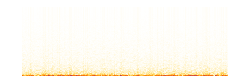

```mathematica
z1State=0;
sampleRate = 48000;
wc = 200;
g=wc/(2sampleRate); (*zavalishin 3.11 *)
G = g/(1+g); (* G = g/(1+g) *)
zavalishinLPF[x_]:=Module[{v,y},
v = (x - z1State)*G;
y = v+ z1State;
z1State = y + v;
y
]

input2 = RandomReal[{-1,1},48000];
zLPFOutput =zavalishinLPF /@ input2; 
ListPlay[zLPFOutput,SampleRate->48000]
Spectrogram[zLPFOutput]
```

## Test Zavalishin First Order Release Filter

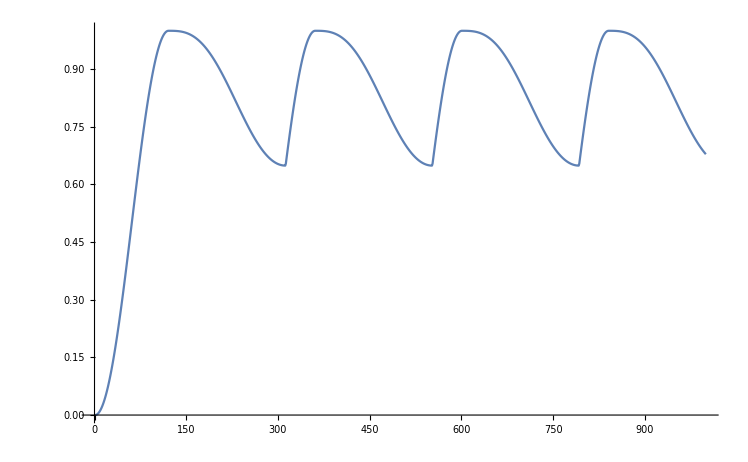

```mathematica
lpfZ1State=0;
lpfG = 0; (* G = g/(1+g) *)
prevOut = 0;

releaseOnly1OrderZavalishinLPF[x_]:=Module[{v,y},
If[x>prevOut,

(* attack state, don't filter *)
y = x;
lpfZ1State = y;
prevOut = y;
,

(* release state, do filter *)
v = (x - lpfZ1State)*lpfG;
y = v+ lpfZ1State;
lpfZ1State = y + v;
prevOut = y;
];

(* output *)
y
]

zLPFSetFc[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
lpfG = g/(1+g);
]

zLPFSetFc[200,48000];
input3Freq = 100;
input3 = Table[Sin[t input3Freq 2 N[π] /48000],{t,0,48000}];
input3 = input3^2;
output3 = releaseOnly1OrderZavalishinLPF /@ input3;
ListLinePlot[output3[[1;;1000]]]
```

## Test Zavalishin First Order AttackFilter

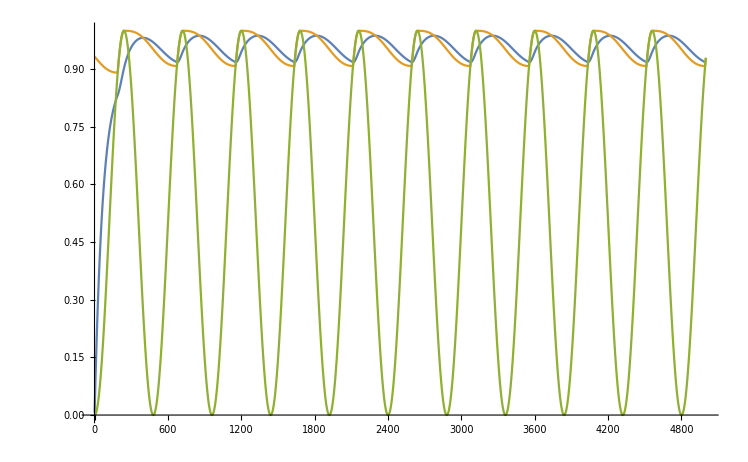

```mathematica
alpfZ1State=0;
alpfG = 0; (* G = g/(1+g) *)
aprevOut = 0;

attackOnly1OrderZavalishinLPF[x_]:=Module[{v,y},
(*If[x>0aprevOut,*)

(* attack state, filter *)
v = (x - alpfZ1State)*alpfG;
y = v+ alpfZ1State;
alpfZ1State = y + v;
aprevOut = y;

(*
,

(* release state, don't filter *)
y = x;
alpfZ1State = y;
aprevOut = y;
];
*)

(* output *)
y
]

azLPFSetFc[fc_,sampleRate_]:=Module[{g},
g =fc / (2 sampleRate); (*zavalishin 3.11 *)
alpfG = g/(1+g);
]

zLPFSetFc[(1/0.050),48000];
azLPFSetFc[(1/0.0015),48000];
input3Freq =50;
input3Length = 5000;
input3 = Table[Sin[t input3Freq 2 N[π] /48000],{t,0,input3Length}];
input3 = input3^2;
output3 = releaseOnly1OrderZavalishinLPF /@ input3;
output32 = attackOnly1OrderZavalishinLPF /@output3;
ListLinePlot[{output32[[1;;input3Length]],output3[[1;;input3Length]],input3[[1;;input3Length]]}]
```

## Test Zavalishin First Order Compressor

```mathematica
sineSweep=LogarithmicSineSweep[20,20000,5,48000];
tone400Hz = Table[Sin[400 2 π / 48000 t],{t,1,48000}];
tone400Hz[[15000;;20000]]=0;
```

```mathematica
focPrevOut = 0;
zFirstOrderCompressor[x_]:=Module[{output,envelope,attenuation=1.0,filterFreq},

(*rectify the previous output *)
envelope=focPrevOut^2;
(* apply release filter to rectified input*)
envelope=releaseOnly1OrderZavalishinLPF[envelope];
(* apply attack filter to rectified input*)
envelope=attackOnly1OrderZavalishinLPF[envelope];

(*apply antialiasing filters*)
(*envelope=compressorSVFLowpass4[compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]];*)
(* envelope=compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]; *)
(* envelope=compressorSVFLowpass2[compressorSVFLowpass1[envelope]]; *)
envelope=compressorSVFLowpass1[envelope];

(* gain calculator *)
(* attenuation=1/(1+50qThreshold[(envelope-compThreshold),0,0.05]);*)
(* attenuation = -qThreshold[-compThreshold/(envelope+0.0001),-1,0.05]; *)
attenuation = 2^(-Max[Log2[envelope+0.00001]-Log2[compThreshold],0]);

(*set the compressor input gain*)
compInputGain=attenuation;

(*apply the input gain*)
output=x*compInputGain;

(* save the output for processing the envelope *)
focPrevOut = output;

(*(*set the filter frequency to attack or release*)If[envelope>prevEnvelope,filterFreq=attackFreq,filterFreq=releaseFreq];
setFcAndQAttachRelease[filterFreq,compQ];*)(*save the previous envelope value*)(*prevEnvelope=envelope;*)(*output*)
output
]


aaFreq=2000;
compQ = 1/8;
attackFreq = (1/0.050);
releaseFreq = (1/0.050);
setFcAndQAAFilters[aaFreq,compQ,48000];
zLPFSetFc[releaseFreq,48000];
azLPFSetFc[attackFreq,48000];
output=zFirstOrderCompressor/@(10sineSweep);
ListLinePlot[output,PlotRange->All]
Export["/Users/hansanderson/Desktop/compressorTest.wav",ListPlay[output,SampleRate->48000,PlayRange->All]];
```

-Graphics-

## Test Zavalishin First Order Attack-Release Filter

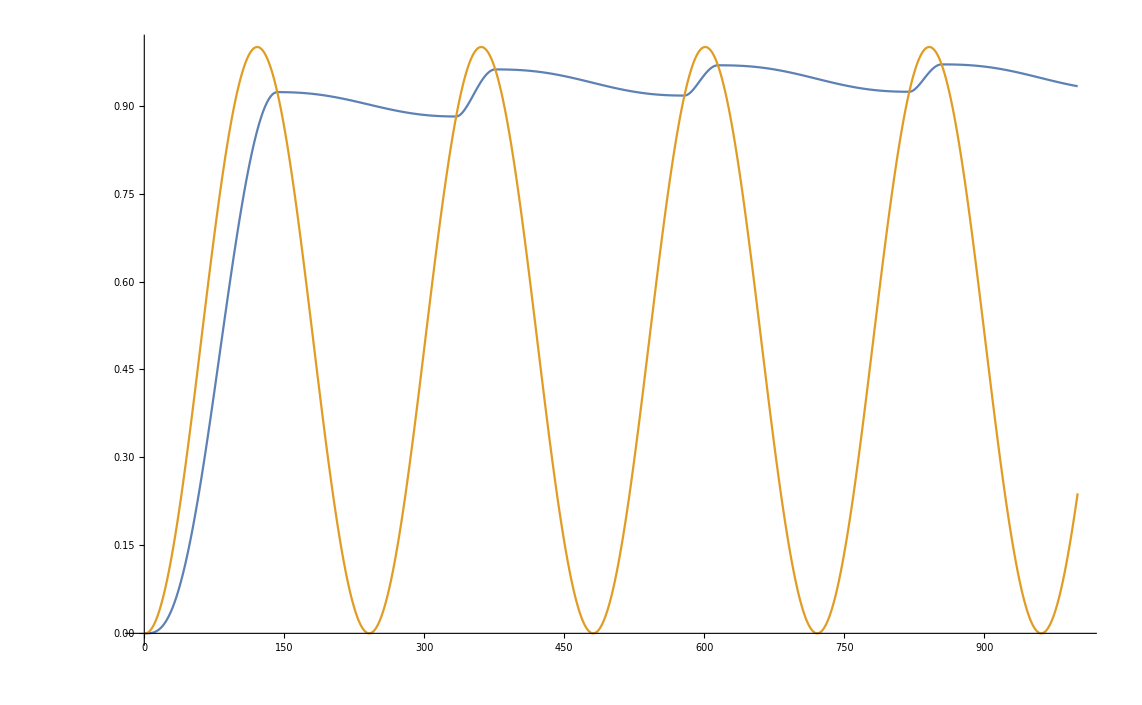

```mathematica
arlpfZ1State=0;
arlpfGAttack = 0; (* G = g/(1+g) *)
arlpfGRelease = 0;
arprevOut = 0;

attackReleaseZavalishinLPF[x_]:=Module[{v,y,g},
If[x>arprevOut,
(* attack state *)
g = arlpfGAttack;
,
(* release state *)
g = arlpfGRelease;
];

(* filter *)
v = (x - arlpfZ1State)*g;
y = v+ arlpfZ1State;
arlpfZ1State = y + v;
arprevOut = y;

(* output *)
y
]

arSetFc[fcAttack_,fcRelease_,sampleRate_]:=Module[{g},
g =fcAttack / (2 sampleRate); (*zavalishin 3.11 *)
arlpfGAttack = g/(1+g);
g =fcRelease/ (2 sampleRate); 
arlpfGRelease = g/(1+g);
]

arSetFc[2000,20,48000];
input3Freq = 100;
input3 = Table[Sin[t input3Freq 2 N[π] /48000],{t,0,48000}];
input3 = input3^2;
output3 = attackReleaseZavalishinLPF /@ input3;
ListLinePlot[{output3[[1;;1000]],input3[[1;;1000]]}]
```

## Test using the Zavalishin Attack-Release filter as an envelope follower for the compressor

```mathematica
ARFeedbackCompressor[x_]:=Module[{output,envelope,attenuation=1.0,filterFreq},
(*apply the input gain*)
output=x*compInputGain;
(*rectify the input*)
envelope=output^2;
(* apply attack-release filter to rectified input*)
envelope=attackReleaseZavalishinLPF[envelope];

(*apply antialiasing filters*)
(*envelope=compressorSVFLowpass4[compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]];*)
(* envelope=compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]; *)
(* envelope=compressorSVFLowpass2[compressorSVFLowpass1[envelope]]; *)
envelope=compressorSVFLowpass1[envelope];

(* gain calculator *)
(* attenuation=1/(1+50qThreshold[(envelope-compThreshold),0,0.05]);*)
(* attenuation = -qThreshold[-compThreshold/(envelope+0.0001),-1,0.05]; *)
attenuation = 2^(-(1/2)Abs[Log2[envelope+0.00001]-Log2[compThreshold]]);

(*set the compressor input gain*)
compInputGain=attenuation;

(*(*set the filter frequency to attack or release*)If[envelope>prevEnvelope,filterFreq=attackFreq,filterFreq=releaseFreq];
setFcAndQAttachRelease[filterFreq,compQ];*)(*save the previous envelope value*)(*prevEnvelope=envelope;*)(*output*)
attenuation
]

arSetFc[450,100,48000];
arlpfZ1State=0.1; (* reset the envelope filter state *)
input=LogarithmicSineSweep[20,20000,5,48000];
aaFreq=1200;
compQ = 1/8;
setFcAndQAAFilters[aaFreq,compQ,48000];
output=ARFeedbackCompressor/@(input);
ListLinePlot[output,PlotRange->{-1,1}]
Export["/Users/hansanderson/Desktop/compressorTest.wav",ListPlay[output,SampleRate->48000,PlayRange->All]];
```

-Graphics-

## Test the attack and release envelope times

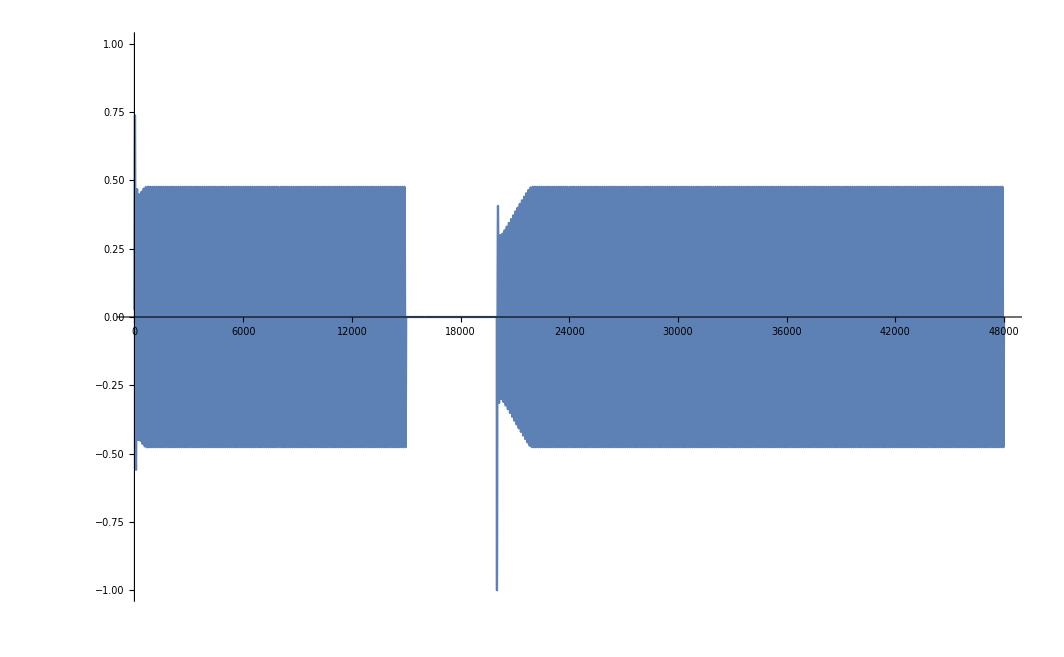

```mathematica
ARFeedbackCompressor[x_]:=Module[{output,envelope,attenuation=1.0,filterFreq},
(*apply the input gain*)
output=x*compInputGain;
(*rectify the input*)
envelope=output^2;
(* apply attack-release filter to rectified input*)
envelope=attackReleaseZavalishinLPF[envelope];

(*apply antialiasing filters*)
(*envelope=compressorSVFLowpass4[compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]];*)
(* envelope=compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]]; *)
(* envelope=compressorSVFLowpass2[compressorSVFLowpass1[envelope]]; *)
envelope=compressorSVFLowpass1[envelope];

(* gain calculator *)
(* attenuation=1/(1+50qThreshold[(envelope-compThreshold),0,0.05]);*)
(* attenuation = -qThreshold[-compThreshold/(envelope+0.0001),-1,0.05]; *)
attenuation = 2^(-Max[Log2[envelope+0.00001]-Log2[compThreshold],0]);

(*set the compressor input gain*)
compInputGain=attenuation;

(*(*set the filter frequency to attack or release*)If[envelope>prevEnvelope,filterFreq=attackFreq,filterFreq=releaseFreq];
setFcAndQAttachRelease[filterFreq,compQ];*)(*save the previous envelope value*)(*prevEnvelope=envelope;*)(*output*)
output
]

arSetFc[(1/0.001),(1/0.050),48000];
arlpfZ1State=0.0; (* reset the envelope filter state *)
input=Table[Sin[400 2 π / 48000 t],{t,1,48000}];
input[[15000;;20000]]=0;
aaFreq=1200;
compQ = 1/8;
setFcAndQAAFilters[aaFreq,compQ,48000];
output=ARFeedbackCompressor/@(input);
ListLinePlot[output,PlotRange->{-1,1}]
Export["/Users/hansanderson/Desktop/compressorTest.wav",ListPlay[output,SampleRate->48000,PlayRange->1.2{-1,1}]];
```

## Write the test input signal to file

```mathematica
Export["/Users/hansanderson/Desktop/compressorTestInput.wav",ListPlay[LogarithmicSineSweep[20,20000,5,48000],SampleRate->48000,PlayRange->All]];
```